```mathematica
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
```

```mathematica
ThermalFidelityXX[ρS_,γ_,T_,Δt_,δ_,nCol_]:=Module[{ω,Ν,γth,J,gDown,gUp,HI,USATotal,U,ρA1,ρA2,ρA,ρS0,ExpandedStates,ReducedStates,g,CanonicalSteadyState,Fidelities},
ω=1;
Ν=1/(Exp[ω/T]-1);
γth=γ(2Ν+1);
J=Sqrt[γth];
HI=-(1/2)J (KronEye[σx,3,1].KronEye[σx,3,2]+KronEye[σy,3,1].KronEye[σy,3,2]);
USATotal=MatrixExp[-ⅈ (HI) Sqrt[Δt]];
U =(SWAP[2,3,3].(PartialSWAP[δ,2,3,3])).USATotal;
g = 1/(2Ν+1);

ρA1=DiagonalMatrix[{(1-g)/2,(1+g)/2}];
ρS0 = kron[ρS,ρA1];
ρA= ρA1;

ExpandedStates=CollisionMap[ρS0,U,ρA1,nCol];
ReducedStates=Table[PTr[ExpandedStates[[i]],{2}],{i,1,Length[ExpandedStates]}];

g = 1/(2Ν+1);
CanonicalSteadyState =DiagonalMatrix[{(1-g)/2,(1+g)/2}];
Fidelities=Chop[Table[QuantumFidelity[ReducedStates[[i]],CanonicalSteadyState],{i,1,Length[ReducedStates]}]]
]
TwoBathFidelityXX[ρS_,γ_,T_,Δt_,δ_,nCol_]:=Module[{ω,Ν,gDown,gUp,HIdown,HIup,USATotal,U,ρA1,ρA2,ρA,ρS0,ExpandedStates,ReducedStates,g,CanonicalSteadyState,Fidelities},
ω=1;
Ν=1/(Exp[ω/T]-1);
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];
HIdown=-(1/2)gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2](*+KronEye[σz,5,1].KronEye[σz,5,2]*));
HIup=-(1/2)gUp (KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3](*+KronEye[σz,5,1].KronEye[σz,5,3]*));
USATotal=MatrixExp[-ⅈ (HIdown+HIup) Sqrt[Δt]];
U =(SWAP[3,5,5].(PartialSWAP[δ,3,5,5])).(SWAP[2,4,5].(PartialSWAP[δ,2,4,5])).USATotal;
ρA1=out[Basis[2,2],Basis[2,2]];
ρA2=out[Basis[2,1],Basis[2,1]];
ρS0 = kron[ρS,ρA1,ρA2];
ρA= kron[ρA1,ρA2];

ExpandedStates=CollisionMap[ρS0,U,ρA,nCol];
ReducedStates=Table[PTr[ExpandedStates[[i]],{2,3}],{i,1,Length[ExpandedStates]}];

g = 1/(2Ν+1);
CanonicalSteadyState =DiagonalMatrix[{(1-g)/2,(1+g)/2}];
Fidelities=Chop[Table[QuantumFidelity[ReducedStates[[i]],CanonicalSteadyState],{i,1,Length[ReducedStates]}]]
]
```

```mathematica
ρS = out[Basis[2,1],Basis[2,1]];
γXX=4;
```

```mathematica
SettingIRedXX = Transpose[{Range[0,3,0.01],1-ThermalFidelityXX[ρS,γXX,0.5,0.01,0.95,Round[3/0.01]]}];SettingIBlueXX = Transpose[{Range[0,3,0.01],1-ThermalFidelityXX[ρS,γXX,0.5,0.01,0.8,Round[3/0.01]]}];
SettingIGrayXX = Transpose[{Range[0,3,0.001],1-ThermalFidelityXX[ρS,γXX,0.5,0.001,0.95,Round[3/0.001]]}];
```

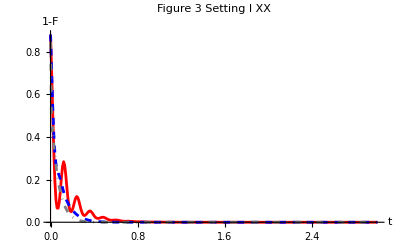

```mathematica
(*Did we mislabel gray and Blue curves in the caption of figure 2? Should be the other way around*)
SettingIXXPlot=ListLinePlot[{SettingIRedXX ,SettingIBlueXX,SettingIGrayXX},PlotRange->All,PlotStyle->{Directive[Red],Directive[Blue,Dashed],Directive[Gray,DotDashed]},PlotLabel-> "Figure 3 Setting I XX",AxesLabel->{"t","1-F"},AxesStyle->Directive[Black,15,FontFamily->"Times New Roman"]]
```

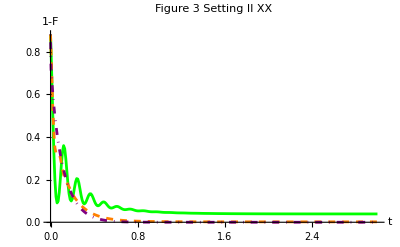

```mathematica
SettingIIRedXX = Transpose[{Range[0,3,0.01],1-TwoBathFidelityXX[ρS,γXX,0.5,0.01,0.95,Round[3/0.01]]}];SettingIIBlueXX = Transpose[{Range[0,3,0.01],1-TwoBathFidelityXX[ρS,γXX,0.5,0.01,0.8,Round[3/0.01]]}];
SettingIIGrayXX = Transpose[{Range[0,3,0.001],1-TwoBathFidelityXX[ρS,γXX,0.5,0.001,0.8,Round[3/0.001]]}];
SettingIIXXPlot=ListLinePlot[{SettingIIRedXX,SettingIIBlueXX,SettingIIGrayXX},PlotRange->All,PlotStyle->{Directive[Green],Directive[Orange,Dashed],Directive[Purple,DotDashed]},PlotLabel-> "Figure 3 Setting II XX",AxesLabel->{"t","1-F"},AxesStyle->Directive[Black,15,FontFamily->"Times New Roman"]]
```

```mathematica
TraceDistanceDifference[ReducedStates1_,ReducedStates2_]:=Block[
{Difference,DifferencesList={},PositiveDifferences,TotalPositiveDifferences},
Do[
Difference=TraceDistance[ReducedStates1[[i+1]],ReducedStates2[[i+1]]]-TraceDistance[ReducedStates1[[i]],ReducedStates2[[i]]];
AppendTo[DifferencesList,Difference];
,{i,1,Length[ReducedStates1]-1}];
PositiveDifferences=Select[DifferencesList,#>0&];
TotalPositiveDifferences=Total[PositiveDifferences];
TotalPositiveDifferences
]

BLPSettingIXX[ρS1_,ρS2_,T_,Δt_,deltas_,TotalTime_]:=Block[{ω,γ,γth,J,Ν,gDown,gUp,HI,USATotal,U,ρA1,ρA2,ρSExpanded1,ρSExpanded2,ρA,nCol,ExpandedStates1,ExpandedStates2,ReducedStates1,ReducedStates2,𝒩,HItotal,SWAP23,g},
ω=1.;
γ=1.;
Ν=1/(Exp[ω/T]-1);
γth=γ(2Ν+1);
J=Sqrt[γth];
HI=-(1/2)J (KronEye[σx,3,1].KronEye[σx,3,2]+KronEye[σy,3,1].KronEye[σy,3,2](*+KronEye[σz,3,1].KronEye[σz,3,2]*));
USATotal=MatrixExp[-ⅈ (HI) Sqrt[Δt]];
g = 1/(2Ν+1);
ρA1=DiagonalMatrix[{(1-g)/2,(1+g)/2}];
ρA= ρA1;
ρSExpanded1 = kron[ρS1,ρA1];
ρSExpanded2 =  kron[ρS2,ρA1];
SWAP23 = N[SWAP[2,3,3]];


ParallelTable[
U =(SWAP23.(PartialSWAP[δ,2,3,3])).USATotal;
nCol = 1000+Round[1/Δt];
ExpandedStates1=CollisionMap[ρSExpanded1,U,ρA,nCol];
ReducedStates1=PTr[#,{2}]&/@ExpandedStates1;
ExpandedStates2=CollisionMap[ρSExpanded2,U,ρA,nCol];
ReducedStates2=PTr[#,{2}]&/@ExpandedStates2;
𝒩=TraceDistanceDifference[ReducedStates1,ReducedStates2]
,{δ,deltas}]
]
BLPSettingIIXX[ρS1_,ρS2_,T_,Δt_,deltas_,TotalTime_]:=Block[{ω,γ,Ν,gDown,gUp,HIdown,HIup,USATotal,U,ρA1,ρA2,ρSExpanded1,ρSExpanded2,ρA,nCol,ExpandedStates1,ExpandedStates2,ReducedStates1,ReducedStates2,𝒩,HItotal,SWAP35,SWAP24},
ω=1.;
γ=1.;
Ν=1/(Exp[ω/T]-1);
gDown=Sqrt[γ (Ν+1)];
gUp=Sqrt[γ (Ν)];
HIdown=-(1/2)gDown (KronEye[σx,5,1].KronEye[σx,5,2]+KronEye[σy,5,1].KronEye[σy,5,2](*+KronEye[σz,5,1].KronEye[σz,5,2]*));
HIup=-(1/2)gUp (KronEye[σx,5,1].KronEye[σx,5,3]+KronEye[σy,5,1].KronEye[σy,5,3](*+KronEye[σz,5,1].KronEye[σz,5,3]*));
HItotal=HIdown+HIup;
ρA1=out[Basis[2,2],Basis[2,2]];
ρA2=out[Basis[2,1],Basis[2,1]];
ρSExpanded1 = kron[ρS1,ρA1,ρA2];
ρSExpanded2 =  kron[ρS2,ρA1,ρA2];
ρA= kron[ρA1,ρA2];
SWAP35 = N[SWAP[3,5,5]];
SWAP24= N[SWAP[2,4,5]];


ParallelTable[
USATotal=MatrixExp[-ⅈ (HItotal) Sqrt[Δt]];
U =(SWAP35.(PartialSWAP[δ,3,5,5])).(SWAP24.(PartialSWAP[δ,2,4,5])).USATotal;
nCol = 1000+Round[1/Δt];
ExpandedStates1=CollisionMap[ρSExpanded1,U,ρA,nCol];
ReducedStates1=PTr[#,{2,3}]&/@ExpandedStates1;
ExpandedStates2=CollisionMap[ρSExpanded2,U,ρA,nCol];
ReducedStates2=PTr[#,{2,3}]&/@ExpandedStates2;
𝒩=TraceDistanceDifference[ReducedStates1,ReducedStates2]
,{δ,deltas}]
]
```

```mathematica
ρg=out[Basis[2,2],Basis[2,2]];
BLPIXXLong=Transpose[{Range[0.8,1,0.001],BLPSettingIXX[ρS,ρg,0.5,0.01,Range[0.8,1,0.001],3]}];
BLPIXXShort=Transpose[{Range[0.8,1,0.001],BLPSettingIXX[ρS,ρg,0.5,0.001,Range[0.8,1,0.001],3]}];
```

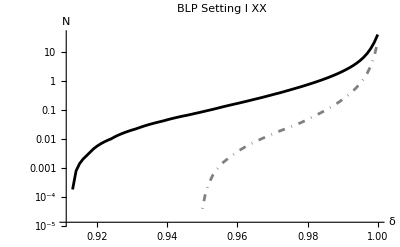

```mathematica
BLPIXXPlot=ListLogPlot[{BLPIXXLong,BLPIXXShort},PlotRange->All,DataRange->{0.8,1},Joined->True,PlotStyle->{Directive[Black],Directive[Gray,DotDashed]},PlotLabel-> "BLP Setting I XX",AxesLabel->{"δ","N"},AxesStyle->Directive[Black,15,FontFamily->"Times New Roman"]]
```

```mathematica
BLPIIXXLong=Transpose[{Range[0.8,1,0.001],BLPSettingIIXX[ρS,ρg,0.5,0.01,Range[0.8,1,0.001],3]}];
BLPIIXXShort = Transpose[{Range[0.8,1,0.001],BLPSettingIIXX[ρS,ρg,0.5,0.001,Range[0.8,1,0.001],3]}];
```

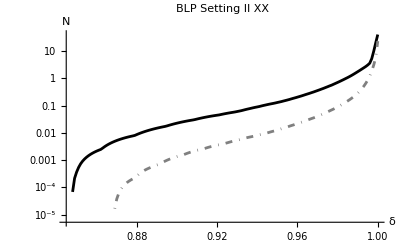

```mathematica
BLPIIXXPlot=ListLogPlot[{BLPIIXXLong,BLPIIXXShort},PlotRange->All,DataRange->{0.8,1},Joined->True,PlotStyle->{Directive[Black],Directive[Gray,DotDashed]},PlotLabel-> "BLP Setting II XX",AxesLabel->{"δ","N"},AxesStyle->Directive[Black,15,FontFamily->"Times New Roman"]]
```